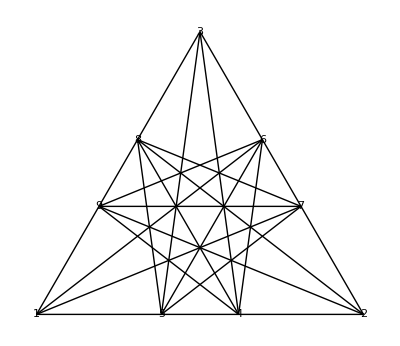

```mathematica
a = {0,0}; b = {1,0};
p = {Cos[60 Degree],Sin[60 Degree]}; 
GRi = 1/GoldenRatio;
points =  {a,b,p,{GRi,0}, {1-GRi,0}, (GRi * (p - b)) + b, ((1-GRi) * (p-b)) + b, (GRi * (p - a)) + a, ((1-GRi) * (p-a)) + a};

Graphics[GraphicsComplex[
points,
{Line[{
{1,2},{2,3},{3,1},
{4,3},{5,3},{6,1}, {7,1},{8,2},{9,2},
{8,7},{7,5},{5,8},{6,4},{4,9},{9,6},
{9,7},{6,5},{8,4}
}], 
Map[Style[Text[#,#], Larger] &, Range[9]]}]]
```

```mathematica
dAngle[v1_, v2_] := N[VectorAngle[points[[v1[[2]]]]-points[[v1[[1]]]],points[[v2[[2]]]]-points[[v2[[1]]]]] /Degree]
```

```mathematica
(* The face defined by the lines {6,1}, {2,8}, {5,3}, {3,4},
the ninth stellation W34 *)
W34 = {dAngle[{3,5}, {3,4}],
dAngle[{4,3}, {6,1}],
dAngle[{6,1}, {8,2}]}
```

{15.5225,120.,104.478}

```mathematica
W34[[1]]/2
180- W34[[3]]/2
```

7.76124

127.761

```mathematica
W34[[1]]*5
```

77.6124